# TES - Response (plot)

## Setup

Loads upstream notebooks and points Direc to ../../input/TES.

```mathematica
nbDir = NotebookDirectory[];
Direc = FileNameJoin[{ParentDirectory[ParentDirectory[nbDir]], "input", "TES"}];
Get[FileNameJoin[{nbDir, "06_response_defs.nb"}]];
SetDirectory[Direc];
Print["Direc = ", Direc];
```

## Response function

### plot

```mathematica
(* function format *)
```

KerR(material) (left/right branch)[DM mass][heavy/light][threshold, uncertainty][vmin]

#### Al

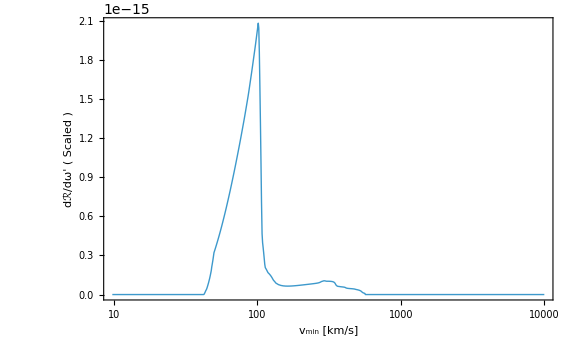
{1.19975,-Graphics-}

```mathematica
AbsoluteTiming[K0AlM10=Plot[
{
-(KerRAll[10MeV][0][0.1 eV,TESsig][vmin kps])+(KerRAlr[10 MeV][0][0.1 eV,TESsig][vmin kps])}
,{vmin,0,10000},
MaxRecursion->0,PlotPoints->800,ScalingFunctions->{"Log"},PlotStyle->{{Thick,ColorData[116,1]},{Dashed,ColorData[116,1]}},
Frame->True,LabelStyle->Directive[FontFamily->"Times",Black,20,Bold],FrameStyle->{Black},
FrameLabel-> {Style["v_min [km/s]",20,SingleLetterItalics->False],Style[" dℛ/dω' ( Scaled )",20],Style["TES, heavy mediator, mχ=10MeV, E_R=0.1eV",20]},
PlotRange->All,ImageSize->Large]]
```

```mathematica
Sqrt[(2 * 1.1360934182590234 eV)/(10MeV) ]* 3 10^5
```

143.002

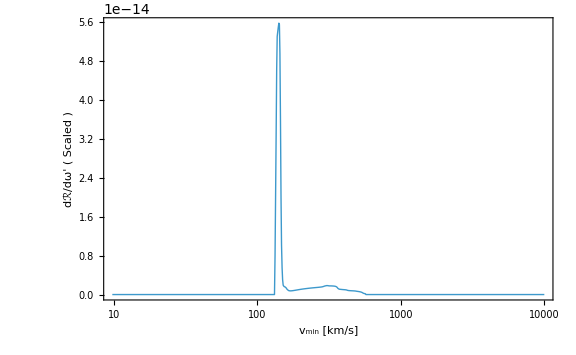
{1.42627,-Graphics-}

```mathematica
AbsoluteTiming[K0AlM10=Plot[
{-(KerRAll[10MeV][0][1 eV,TESsig][vmin kps])+
(KerRAlr[10 MeV][0][1 eV,TESsig][vmin kps])}
,{vmin,0,10000},
MaxRecursion->0,PlotPoints->800,ScalingFunctions->{"Log"},PlotStyle->{{Thick,ColorData[116,1]},{Dashed,ColorData[116,1]}},
Frame->True,LabelStyle->Directive[FontFamily->"Times",Black,20,Bold],FrameStyle->{Black},
FrameLabel-> {Style["v_min [km/s]",20,SingleLetterItalics->False],Style[" dℛ/dω' ( Scaled )",20],Style["TES, heavy mediator, mχ=10MeV, E_R=1eV",20]},
PlotRange->All,ImageSize->Large]]
```

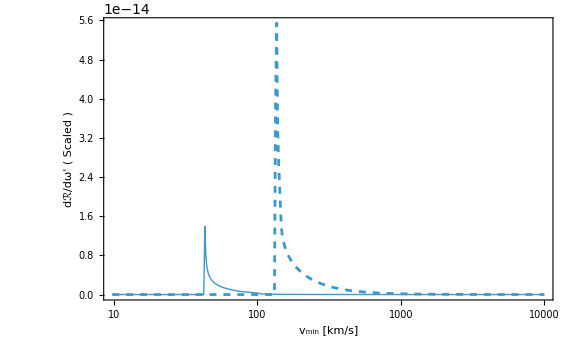
{1.44585,-Graphics-}

```mathematica
AbsoluteTiming[K2AlM10=Plot[
{
(KerRAll[10MeV][2][0.1,TESsig*.1][vmin kps]+KerRAlr[10 MeV][2][0.1,TESsig*.1][vmin kps]),
(KerRAll[10 MeV][2][1,TESsig*1][vmin kps]+KerRAlr[10 MeV][2][1,TESsig*1][vmin kps])}
,{vmin,0,10000},
MaxRecursion->0,PlotPoints->800,ScalingFunctions->{"Log"},PlotStyle->{{Thick,ColorData[116,1]},{Dashed,ColorData[116,1]}},
Frame->True,LabelStyle->Directive[FontFamily->"Times",Black,20,Bold],FrameStyle->{Black},
FrameLabel-> {Style["v_min [km/s]",20,SingleLetterItalics->False],Style[" dℛ/dω' ( Scaled )",20],Style["TES, light mediator",20]},
PlotRange->All,ImageSize->Large]]
```

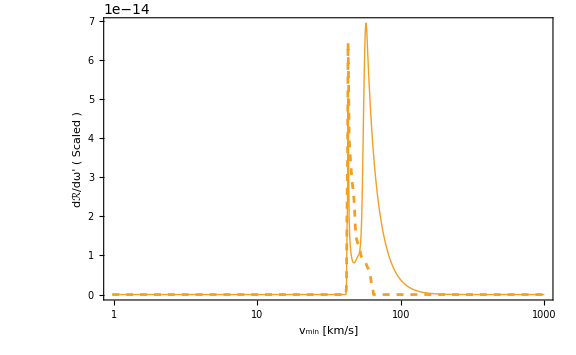
{0.942265,-Graphics-}

```mathematica
AbsoluteTiming[K0AlM100=Plot[
{KerRAll[100 MeV][0][1,TESsig*1][vmin kps], 
KerRAlr[100 MeV][0][1,TESsig*1][vmin kps]}
,{vmin,0,1000},
MaxRecursion->0,PlotPoints->800,ScalingFunctions->{"Log"},PlotStyle->{{Thick,ColorData[116,2]},{Dashed,ColorData[116,2]}},
Frame->True,LabelStyle->Directive[FontFamily->"Times",Black,20,Bold],FrameStyle->{Black},
FrameLabel-> {Style["v_min [km/s]",20,SingleLetterItalics->False],Style[" dℛ/dω' ( Scaled )",20],Style["TES, heavy mediator, mχ=100MeV, E_R=0.1eV",20]},
PlotRange->All,ImageSize->Large]]
```

```mathematica
AbsoluteTiming[K0AlM100=Plot[
{KerRAll[100 MeV][0][1,TESsig*1][vmin kps], 
KerRAlr[100 MeV][0][1,TESsig*1][vmin kps]}
,{vmin,0,1000},
MaxRecursion->0,PlotPoints->800,ScalingFunctions->{"Log"},PlotStyle->{{Thick,ColorData[116,2]},{Dashed,ColorData[116,2]}},
Frame->True,LabelStyle->Directive[FontFamily->"Times",Black,20,Bold],FrameStyle->{Black},
FrameLabel-> {Style["v_min [km/s]",20,SingleLetterItalics->False],Style[" dℛ/dω' ( Scaled )",20],Style["TES, heavy mediator, mχ=100MeV, E_R=1eV",20]},
PlotRange->All,ImageSize->Large]]
```

{0.936108,-Graphics-}

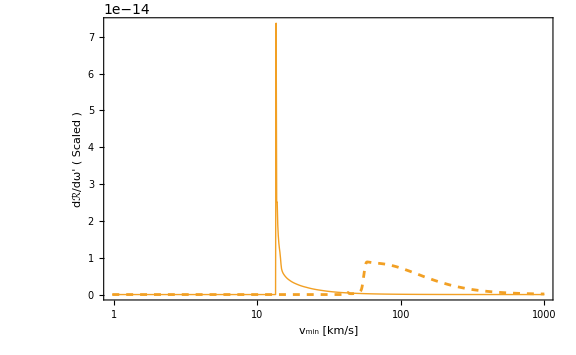
{1.03148,-Graphics-}

```mathematica
AbsoluteTiming[K2AlM100=Plot[
{
(KerRAll[100MeV][2][0.1,TESsig*.1][vmin kps]+KerRAlr[100 MeV][2][0.1,TESsig*.1][vmin kps]),
(KerRAll[100 MeV][2][1,TESsig*1][vmin kps]+KerRAlr[100 MeV][2][1,TESsig*1][vmin kps])}
,{vmin,0,1000},
MaxRecursion->0,PlotPoints->800,ScalingFunctions->{"Log"},PlotStyle->{{Thick,ColorData[116,2]},{Dashed,ColorData[116,2]}},
Frame->True,LabelStyle->Directive[FontFamily->"Times",Black,20,Bold],FrameStyle->{Black},
FrameLabel-> {Style["v_min [km/s]",20,SingleLetterItalics->False],Style[" dℛ/dω' ( Scaled )",20],Style["TES, light mediator",20]},
PlotRange->All,ImageSize->Large]]
```

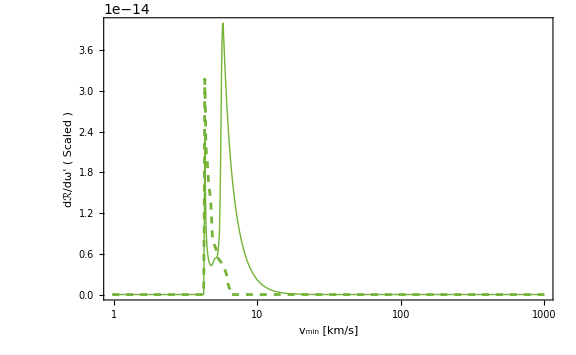
{0.161394,-Graphics-}

```mathematica
AbsoluteTiming[K0AlM1000=Plot[
{
(KerRAll[1000 MeV][0][0.1,TESsig*.1][vmin kps]),(KerRAlr[1000 MeV][0][0.1,TESsig*.1][vmin kps])}
,{vmin,0,1000},
MaxRecursion->0,PlotPoints->800,ScalingFunctions->{"Log"},PlotStyle->{{Thick,ColorData[116,3]},{Dashed,ColorData[116,3]}},
Frame->True,LabelStyle->Directive[FontFamily->"Times",Black,20,Bold],FrameStyle->{Black},
FrameLabel-> {Style["v_min [km/s]",20,SingleLetterItalics->False],Style[" dℛ/dω' ( Scaled )",20],Style["TES, heavy mediator, mχ=1GeV, E_R=0.1eV",20]},
PlotRange->All,ImageSize->Large]]
```

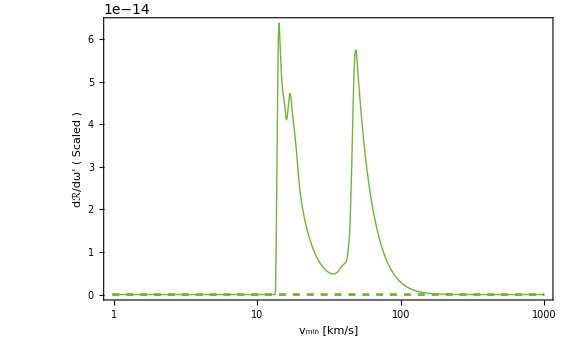
{1.28268,-Graphics-}

```mathematica
AbsoluteTiming[K0AlM1000=Plot[
{(KerRAll[1000 MeV][0][1,TESsig*1][vmin kps]),
(KerRAlr[1000 MeV][0][1,TESsig*1][vmin kps])}
,{vmin,0,1000},
MaxRecursion->0,PlotPoints->800,ScalingFunctions->{"Log"},PlotStyle->{{Thick,ColorData[116,3]},{Dashed,ColorData[116,3]}},
Frame->True,LabelStyle->Directive[FontFamily->"Times",Black,20,Bold],FrameStyle->{Black},
FrameLabel-> {Style["v_min [km/s]",20,SingleLetterItalics->False],Style[" dℛ/dω' ( Scaled )",20],Style["TES, heavy mediator, mχ=1GeV, E_R=1eV",20]},
PlotRange->All,ImageSize->Large]]
```

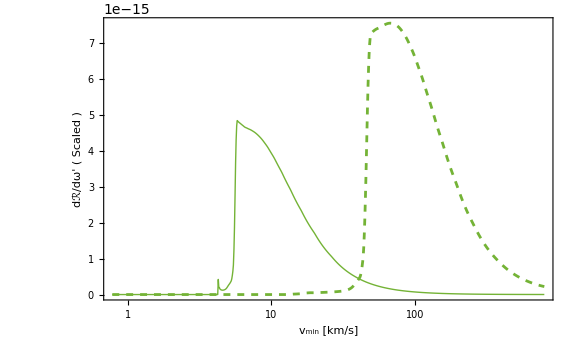
{1.28539,-Graphics-}

```mathematica
AbsoluteTiming[K2AlM1000=Plot[
{
(KerRAll[1000 MeV][2][0.1,TESsig*.1][vmin kps]+KerRAlr[1000 MeV][2][0.1,TESsig*.1][vmin kps]),
(KerRAll[1000 MeV][2][1,TESsig*1][vmin kps]+KerRAlr[1000 MeV][2][1,TESsig*1][vmin kps])}
,{vmin,0,800},
MaxRecursion->0,PlotPoints->800,ScalingFunctions->{"Log"},PlotStyle->{{Thick,ColorData[116,3]},{Dashed,ColorData[116,3]}},
Frame->True,LabelStyle->Directive[FontFamily->"Times",Black,20,Bold],FrameStyle->{Black},
FrameLabel-> {Style["v_min [km/s]",20,SingleLetterItalics->False],Style[" dℛ/dω' ( Scaled )",20],Style["TES, light mediator",20]},
PlotRange->All,ImageSize->Large]]
```

#### Result

```mathematica
(* Depends on how we want to combine the plots *)
```

```mathematica
(* Al,Heavy *)
```

```mathematica
line1=Plot[.175,{x,.8,1.2},ScalingFunctions->{"Log"},PlotStyle->{Black}];
line2=Plot[.095,{x,.8,1.2},ScalingFunctions->{"Log"},PlotStyle->{Black,Dashed}];
K0Al=Show[K0AlM10,K0AlM100,K0AlM1000,line1,line2,Epilog->{
Inword["ω'"][20][.16,.36][{Black,Bold}],
Inword["0.1 eV"][18][.24,.3][Black],
Inword["1 eV"][18][.228,.24][Black],
Inword["m_χ"][20][.89,.85][Black],
Inword["10^1 MeV"][18][.89,.78][ColorData[116,1]],
Inword["10^2 MeV"][18][.89,.72][ColorData[116,2]],
Inword["10^3 MeV"][18][.89,.66][ColorData[116,3]]
}]
```

```mathematica
(* Al,Light *)
```

```mathematica
line1=Plot[.175,{x,.8,1.2},ScalingFunctions->{"Log"},PlotStyle->{Black}];
line2=Plot[.095,{x,.8,1.2},ScalingFunctions->{"Log"},PlotStyle->{Black,Dashed}];
K2Al=Show[K2AlM10,K2AlM100,K2AlM1000,line1,line2,Epilog->{
Inword["ω'"][20][.16,.36][{Black,Bold}],
Inword["0.1 eV"][18][.24,.3][Black],
Inword["1 eV"][18][.228,.24][Black],
Inword["m_χ"][20][.89,.85][Black],
Inword["10^1 MeV"][18][.89,.78][ColorData[116,1]],
Inword["10^2 MeV"][18][.89,.72][ColorData[116,2]],
Inword["10^3 MeV"][18][.89,.66][ColorData[116,3]]
}]
```

```mathematica
(* TiN,Heavy *)
```

```mathematica
line1=Plot[.175,{x,.8,1.2},ScalingFunctions->{"Log"},PlotStyle->{Black}];
line2=Plot[.095,{x,.8,1.2},ScalingFunctions->{"Log"},PlotStyle->{Black,Dashed}];
K0TiN=Show[K0TiNM10,K0TiNM100,K0TiNM1000,line1,line2,Epilog->{
Inword["ω'"][20][.16,.36][{Black,Bold}],
Inword["0.1 eV"][18][.24,.3][Black],
Inword["1 eV"][18][.228,.24][Black],
Inword["m_χ"][20][.89,.85][Black],
Inword["10^1 MeV"][18][.89,.78][ColorData[116,1]],
Inword["10^2 MeV"][18][.89,.72][ColorData[116,2]],
Inword["10^3 MeV"][18][.89,.66][ColorData[116,3]]
}]
```

```mathematica
(* TiN,Light *)
```

```mathematica
line1=Plot[.175,{x,.8,1.2},ScalingFunctions->{"Log"},PlotStyle->{Black}];
line2=Plot[.095,{x,.8,1.2},ScalingFunctions->{"Log"},PlotStyle->{Black,Dashed}];
K2TiN=Show[K2TiNM10,K2TiNM100,K2TiNM1000,line1,line2,Epilog->{
Inword["ω'"][20][.16,.36][{Black,Bold}],
Inword["0.1 eV"][18][.24,.3][Black],
Inword["1 eV"][18][.228,.24][Black],
Inword["m_χ"][20][.89,.85][Black],
Inword["10^1 MeV"][18][.89,.78][ColorData[116,1]],
Inword["10^2 MeV"][18][.89,.72][ColorData[116,2]],
Inword["10^3 MeV"][18][.89,.66][ColorData[116,3]]
}]
```

```mathematica
Export[FileNameJoin[Direc,"Alq0.pdf"],K0Al]
Export[FileNameJoin[Direc,"Alq2.pdf"],K2Al]
```

```mathematica
Export[FileNameJoin[Direc,"TiNq0.pdf"],K0TiN]
Export[FileNameJoin[Direc,"TiNq2.pdf"],K2TiN]
```